```mathematica
(* import video *)
filename="/Users/asudler/Desktop/OU/coursework/2023/fall/PHYS-3302-ALAB1/cavendish/data-mathematica/runs/run4/run4.mov";
frames=Import[filename,"ImageList"];
```

```mathematica
(* find good cropping dimensions *)
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
(* crop frames *)
length=Length[frames];
ymin=232;
ymax=360;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
croppedFrames[[1]]
```

-Graphics-

```mathematica
length
```

677

```mathematica
(* binarize data *)
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
(* get center pixel coordinates *)
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

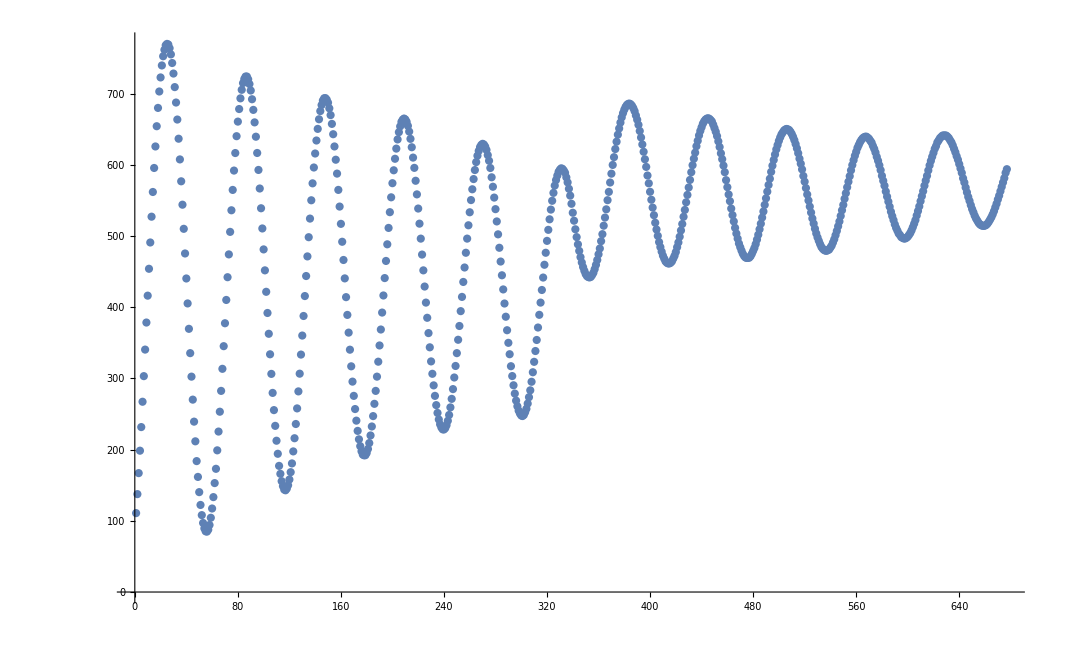

```mathematica
ListPlot[Transpose[xvals]]
```

```mathematica
(* we need to figure out two things: (1) the time between frames, and (2) what each pixel represents in length *)
(* we will start with time. notice how it is hard to see the anything beyond the seconds position on the image below *)
frames[[1]]
```

-Graphics-

```mathematica
(* so, let's look at the first time and the last time and calculate dt from there *)
frames[[-1]]
```

-Graphics-

```mathematica
1*60*60+30*60+32
```

5432

```mathematica
(5432.6-24.6)/length
```

7.98818

```mathematica
(* so dt = 7.98818 seconds. then we set up the time scale of our graph by multiplying the frame number by 7.98818 *)
tvals=Table[i*7.98818,{i,length}];
```

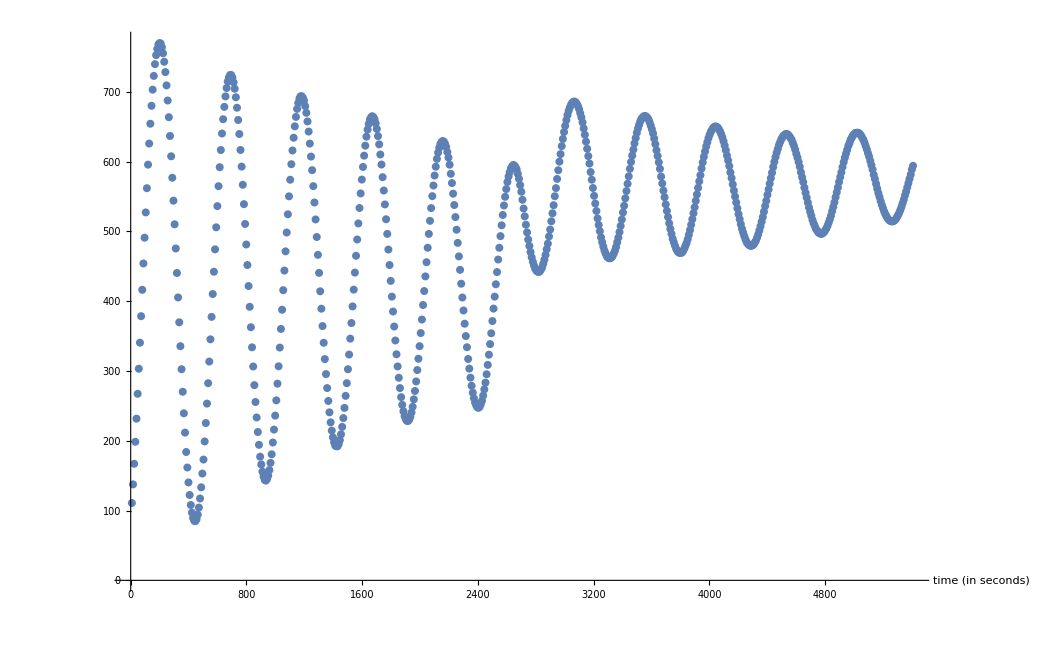

```mathematica
(* with this in mind, our plot now looks like: *)
ListPlot[Transpose[{tvals,xvals}],AxesLabel->{"time (in seconds)"}]
```

```mathematica
(* how do we get the length scale? *)
(* we will have to import our reference video we took where we have an item of known length (a sheet of paper) taped to the blackboard. we can then see how this length translates into pixels *)
(* import reference video *)
filenameGrid="/Users/asudler/Desktop/OU/coursework/2023/fall/PHYS-3302-ALAB1/cavendish/data-mathematica/runs/run4/run4_grid.MOV";
framesGrid=Import[filenameGrid,"ImageList"];
```

```mathematica
framesGrid[[1]]
```

-Graphics-

```mathematica
(* find good cropping dimensions *)
Manipulate[ImageTake[framesGrid[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
(* in this one I am specifically trying to get the horizontal length, and the paper is slightly tilted, so I am looking at a constant y value across the top edge of the paper*)
```

```mathematica
paperRef=ImageTake[framesGrid[[1]],{192,326},{759,919}]
```

-Graphics-

```mathematica
(* this is not exact since part of the left side is slighly cut off and part of the right side has the blackboard. but hopefully this will get us close enough *)
(* so it seems that our video is not exactly vertically aligned... but that's ok... maybe .... *)
paperDims=ImageDimensions[paperRef]
```

{161,135}

```mathematica
0.2794/161
```

0.0017354

```mathematica
(* our direction of interest, the horizontal direction, is 11 inches = 0.2794 meters. so 161 pixels = 0.2794m -> 0.00174625 m/pixel *)
conv=0.0017354037267080743;
```

```mathematica
(* converting *)
posvals=Table[xvals[[i]]*conv,{i,length}];
```

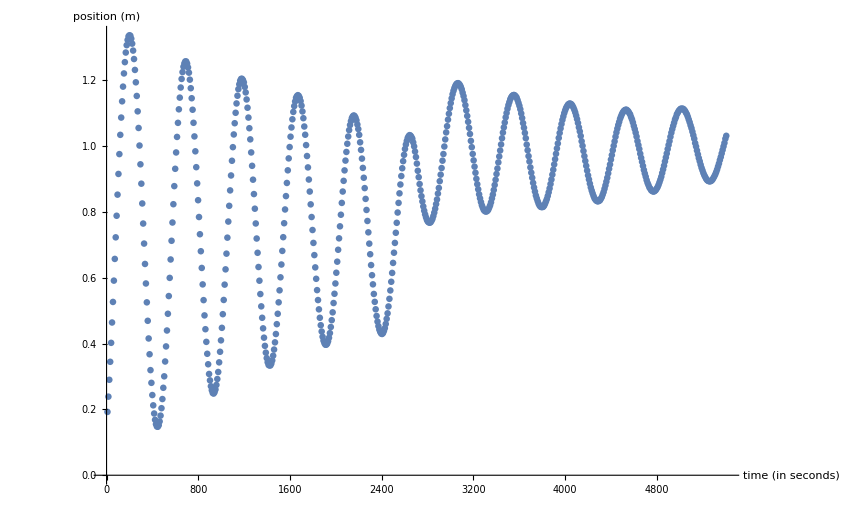

```mathematica
(* plotting *)
ListPlot[Transpose[{tvals,posvals}],AxesLabel->{"time (in seconds)","position (m)"}]
```

```mathematica
(* yippee! this look awesome! let's export *)
Export["/Users/asudler/Desktop/laser_pos_v_time_run4.csv",Transpose[{tvals,posvals}]]
```

/Users/asudler/Desktop/laser_pos_v_time_run4.csv